```mathematica
<<TRQS`
```

Package TRQS version 0.0.8 (last modification: February 22, 2011).

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/jam/Kuweta/notatki/programming/mathematica/TRQS

```mathematica
maxN = 7;
```

```mathematica
quantisNoHW=Table[{ii,AbsoluteTiming[Table[TrueRandomReal[],{10^ii}];][[1]]},{ii,1,maxN}]
Export["quantisNoHW.dat",quantisNoHW]
```

$Aborted

```mathematica
quantisNoHW=Import["quantisNoHW.dat"]
```

{{1,0.000365},{2,0.002844},{3,0.031761},{4,0.278536},{5,2.09595},{6,18.1517},{7,205.171}}

```mathematica
pseudo=Table[{ii,AbsoluteTiming[Table[RandomReal[];ClearSystemCache["Numeric"],{10^ii}];][[1]]},{ii,1,maxN}];
Export["pseudo.dat",pseudo]
```

pseudo.dat

```mathematica
pseudo=Import["pseudo.dat"]
```

{{1,0.000052},{2,0.000268},{3,0.003889},{4,0.033749},{5,0.299357},{6,2.99425},{7,29.3132}}

## Prawdziwy Quantis

```mathematica
quantis=Table[{ii,AbsoluteTiming[Table[TrueRandomReal[],{10^ii}];][[1]]},{ii,1,maxN}]
Export["quantis.dat",quantis]
```

{{1,0.10366},{2,0.999978},{3,10.27994},{4,100.20004},{5,1001.41028},{6,10012.10371},{7,60738.7188}}

quantis.dat

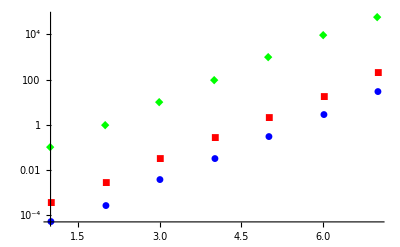

```mathematica
ListLogPlot[{pseudo,quantisNoHW,quantis},Joined->False,PlotStyle->{Blue,Red,Green},PlotMarkers->Automatic]
```

```mathematica
Log10[80000]//N
```

4.90309